```mathematica
ClearAll["Global`*"]
```

### Equation (11) from Dors and Kletzing [1999]

Tm in eV
dens_m in cm^-3
pot in eV
RB the mirror ratio

```mathematica
speedOfLight=299792458;
inMass=5.1099891*^5/speedOfLight^2;
eCharge=1.602*^-19;
```

```mathematica
jDors[kappa_,Tm_,densm_,pot_,RB_]:= eCharge (1*^6 densm )√((Tm(1-3/(2 kappa)))/(2 π inMass))kappa/(kappa-1)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])RB(1-(1-1/RB)(1+(pot/Tm)/((kappa-3/2)(RB-1)))^(1-kappa));
jDorsPotBar[kappa_,Tm_,densm_,potBar_,RB_]:= eCharge (1*^6 densm )√((Tm(1-3/(2 kappa)))/(2 π inMass))kappa/(kappa-1)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])RB(1-(1-1/RB)(1+potBar/((kappa-3/2)(RB-1)))^(1-kappa));
```

#### Barbosa [1977] equations, updated for kappa

```mathematica
vbOverw[deltaPhi_,T_,kappa_]:=√(deltaPhi/(T (1-3/(2 kappa))));
normK[deltaPhi_,T_,kappa_]:=2/π^(1/2)(kappa^(1/2)/2 Gamma[kappa-1/2]/Gamma[kappa]+√(deltaPhi/(π T (1-3/(2kappa))))Hypergeometric2F1[1/2,kappa,3/2,-deltaPhi/(T (kappa-3/2))])^-1;
barbKappa[vpar_,vperp_,deltaPhi_,T_,kappa_,alpha_]:= (1+(vpar^2+vperp^2+(vbOverw[deltaPhi,T,kappa])^2-2 (vbOverw[deltaPhi,T,kappa])(vpar^2+vperp^2(1-alpha))^(1/2))/kappa)^(-(kappa+1))UnitStep[vpar];
```

```mathematica
barb[α_,vOvera_]:=1+(2(1-α)vOvera Exp[-α vOvera^2])/Erfc[-vOvera] NIntegrate[Exp[α x^2]Erfc[x],{x,-vOvera,∞}];
barbK[alpha_,deltaPhi_,T_,kappa_]:=normK[deltaPhi,T,kappa] NIntegrate[vperp barbKappa[vpar,vperp,deltaPhi,T,kappa,alpha],{vpar,0,∞},{vperp,0,∞}];
```

Input data for computation of reduced chi-squared

```mathematica
medianPotAbove=941;
meanPotAbove=948;
pAbove=medianPotAbove;
TFAST=110.2; (*eV*)
nFAST = 1.88;(*cm^-3*)
```

```mathematica
TandNString=ToString[StringForm["TFAST_eq_`1`-nFAST_eq_`2`",NumberForm[TFAST,{4,1},NumberPoint->"_"],NumberForm[nFAST,3,NumberPoint->"_"]]];
```

```mathematica
mapKappaList={1.505,1.510,1.515,1.520,1.525,1.530,1.535,1.540,1.545,1.550,1.555,1.560,1.565,1.570,1.575,1.580,1.585,1.590,1.595,1.600,1.605,1.610,1.615,1.620,1.625,1.630,1.635,1.640,1.645,1.650,1.655,1.660,1.665,1.670,1.675,1.680,1.685,1.690,1.695,1.700,1.705,1.710,1.715,1.720,1.725,1.730,1.735,1.740,1.745,1.750,1.755,1.760,1.765,1.770,1.775,1.780,1.785,1.790,1.795,1.800,1.805,1.810,1.815,1.820,1.825,1.830,1.835,1.840,1.845,1.850,1.855,1.860,1.865,1.870,1.875,1.880,1.885,1.890,1.895,1.900,1.905,1.910,1.915,1.920,1.925,1.930,1.935,1.940,1.945,1.950,1.955,1.960,1.965,1.970,1.975,1.980,1.985,1.990,1.995,2.000,2.050,2.100,2.200,2.300,2.400,2.500,2.600,2.700,2.800,2.900,3.000,3.250,3.500,3.750,4.000,4.250,4.500,4.750,5.000,5.250,5.500,5.750,6.000,6.250,6.500,6.750,7.000,7.250,7.500,7.750,8.000};
mapRBList =Flatten[{PowerRange[5,1*^4,1.05],1*^4}];
lenRB=Length[mapRBList];
lenKappa=Length[mapKappaList];
StringForm["N elem to compute: `1` (`2`, `3`)",lenKappa*lenRB,lenKappa,lenRB]
```

N elem to compute: 20567 (131, 157)

#### Open ze file

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/";
(*fil=FileNameJoin[{dir,"kappaBarbosaFacs.txt"}]*)
```

```mathematica
(*outStream=OpenWrite[fil]*)
```

```mathematica
(*Close[outStream];*)
```

```mathematica
(*FilePrint[fil]*)
```

#### Just to see if we can print

```mathematica
listKRun=lenKappa;listRRun=lenRB;
```

```mathematica
listKRun=2;listRRun=4;
```

```mathematica
For[iK=1,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaBarbosaFacs_`1`_of_`2`.txt",iK,listKRun]]}];Print[tmpFile];outStream=OpenWrite[tmpFile];For[iR=1,iR≤listRRun,iR++,WriteString[outStream,StringForm["`1`,`2`,`3`,`4`,`5`,`6`\n",(iK-1)*lenRB+iR,iK,iR,NumberForm[mapKappaList[[iK]],{4,3}],NumberForm[mapRBList[[iR]],{4,1}],"BRO"]]];Close[outStream]]
```

```mathematica
For[iK=1,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaBarbosaFacs_`1`_of_`2`.txt",iK,listKRun]]}];Print[tmpFile];Print["\n"];FilePrint[tmpFile]]
```

#### Now the real thing

```mathematica
listKRun=lenKappa;listRRun=lenRB;
```

```mathematica
listKRun=2;listRRun=4;
```

```mathematica
For[iK=99,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaBarbosaFacs-`1`--`2`_of_`3`.txt",TandNString,iK,listKRun]]}];Print[tmpFile];
Unprotect[outStream];Clear[outStream];
outStream=OpenWrite[tmpFile];For[iR=1,iR≤listRRun,iR++,WriteString[outStream,StringForm["`1`,`2`,`3`,`4`,`5`,`6`\n",(iK-1)*lenRB+iR,iK,iR,NumberForm[mapKappaList[[iK]],{4,3}],NumberForm[mapRBList[[iR]],{4,1}],NumberForm[barbK[1/mapRBList[[iR]],√(pAbove/TFAST),mapKappaList[[iK]]],6]]]];Close[outStream]]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--99_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--100_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--101_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--102_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--103_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--104_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--105_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--106_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--107_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--108_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--109_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--110_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--111_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--112_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--113_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--114_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--115_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--116_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--117_of_131.txt

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--118_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--119_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--120_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--121_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--122_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--123_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--124_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--125_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--126_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--127_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--128_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--129_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--130_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88--131_of_131.txt

```mathematica
For[iK=1,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaBarbosaFacs-`1`--`2`_of_`3`.txt",TandNString,iK,listKRun]]}];Print[tmpFile];FilePrint[tmpFile]]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88-1_of_2.txt

1,1,1,1.505,5.0,4.55599
2,1,2,1.505,5.2,4.71623
3,1,3,1.505,5.5,4.87838
4,1,4,1.505,5.8,5.04224
158,2,1,1.510,5.0,4.56069
159,2,2,1.510,5.2,4.72121
160,2,3,1.510,5.5,4.88363
161,2,4,1.510,5.8,5.04777

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaBarbosaFacs-TFAST_eq_110_2-nFAST_eq_1_88-2_of_2.txt

## Plot Figure 2 in Dors and Kletzing [1999]

```mathematica
kappaList={1000,10,5,3,2,1.6};
RBList={3,10,30,100,1000};
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
tick=0.002;
kappaStyles={Directive[Dashing[{0,0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[GrayLevel[grayLev2],Thickness[tick]]};
```

```mathematica
T=110;
n=1;
```

```mathematica
jDors[10,T,n,1000,5]
```

1.25371×10^-6

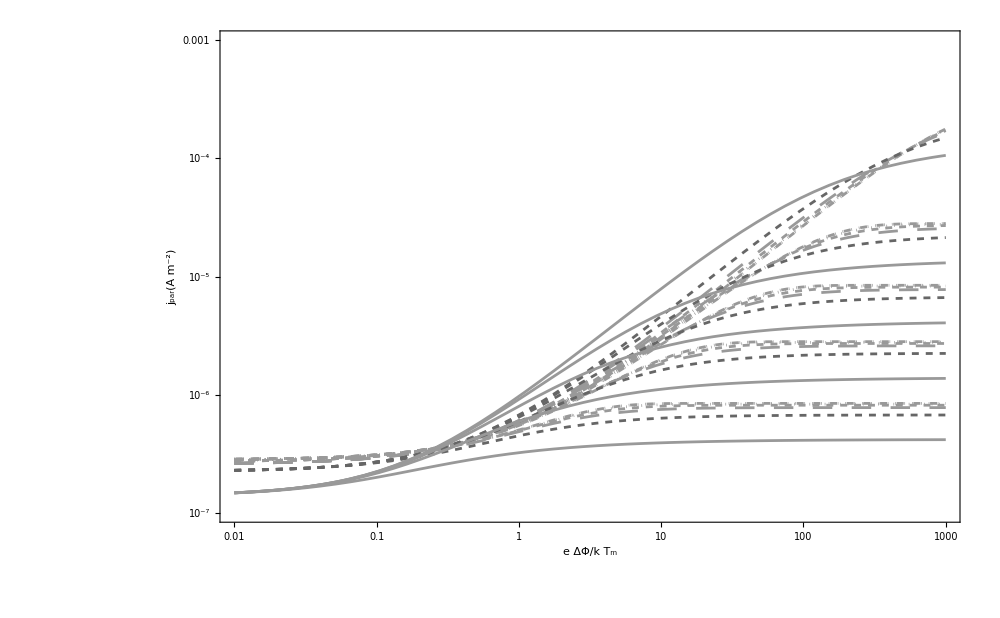

```mathematica
Show[Table[LogLogPlot[jDorsPotBar[kappaList[[j]],T,n,potBar,RBList[[k]]],{potBar,0.01,1000},PlotRange->{{0.01,1000},{1*^-7,1*^-3}},Frame->True,ImageSize->1000,FrameLabel->{StringForm["e ΔΦ/k T_m"],StringForm["j_par(A m^-2)"]},LabelStyle->(FontSize->18),PlotStyle->kappaStyles[[j]] ],{j,1,6},{k,1,5}]]
```